```mathematica
parse[s_]:=ToExpression@StringReplace[s,{" "->"", "("->"{",")"->"}","Vector("->"{","E"->"*10^"}]
```

```mathematica
model=a x^n+c;
```

```mathematica
(*model=a n^x+c;*)
```

```mathematica
fitDegree[data_]:=FindFit[data,model,{a,n,c},x]
```

```mathematica
plotTogehter[data_, rule_]:=With[{expr=model/.rule},
Show[
Plot[expr,{x,data[[1,1]],data[[-1,1]]}],
ListPlot[data,PlotStyle->Red],PlotLabel->expr]]
```

```mathematica
fitAndPlot[data_]:=plotTogehter[data,fitDegree[data]]
```

```mathematica
s=ReadString[NotebookDirectory[]<> "FitterData.txt"];
```

FindFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

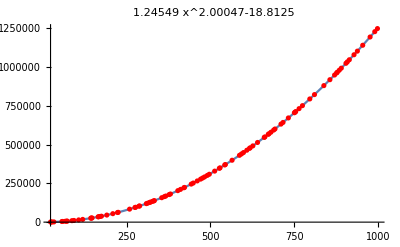

```mathematica
fitAndPlot[parse[s]]
```